```mathematica
(* Metric *)
gcov=DiagonalMatrix[{-(1-2/r),r/(r-2),r^2,r^2 Sin[theta]^2}];
gcon=FullSimplify[Inverse[gcov]];
MatrixForm[gcov]
MatrixForm[gcon]

(* Boosts vector au from the frame moving at velocity wu to frame moving at velocity uu *)
LorentzBoostUpper[au_,uu_,ud_,wu_,wd_]:=Block[{lorentzgam,Omeg,OmegSq,Lam},lorentzgam=-wu.ud;Omeg=Table[uu[[mu]]wd[[nu]]-wu[[mu]]ud[[nu]],{mu,1,4},{nu,1,4}]//.consts;OmegSq=Table[Sum[Omeg[[mu,sigma]]Omeg[[sigma,nu]],{sigma,1,4}],{mu,1,4},{nu,1,4}];Lam=IdentityMatrix[4]+OmegSq/(lorentzgam+1)+Omeg;Lam.au];
InverseLorentzBoostUpper[au_,uu_,ud_,wu_,wd_]:=Block[{neguu,negud},neguu=-uu; neguu[[1]]=-neguu[[1]];negud=-ud; negud[[1]]=-negud[[1]];LorentzBoostUpper[au,neguu,negud,wu,wd]];

InverseLorentzBoostLower[ad_,uu_,ud_,wu_,wd_]:=Block[{neguu,negud},neguu=-uu; neguu[[1]]=-neguu[[1]];negud=-ud; negud[[1]]=-negud[[1]];LorentzBoostLower[ad,neguu,negud,wu,wd]];

LorentzBoostLower[ad_,uu_,ud_,wu_,wd_]:=LorentzBoostUpper[ad,ud,uu,wd,wu];

vel3p2vel3u[vel3phys_]:={1,Sqrt[gcon[[2,2]]]Sqrt[-gcov[[1,1]]] vel3phys[[2]],Sqrt[gcon[[3,3]]] Sqrt[-gcov[[1,1]]]vel3phys[[3]],Sqrt[gcon[[4,4]]]Sqrt[-gcov[[1,1]]] vel3phys[[4]]};

vel3u2vel4u[vel3u_]:=Block[{uut},uut=1/(-gcov[[1,1]]-Sum[gcov[[i,i]] vel3u[[i]]^2,{i,2,4}])^(1/2); vel3u uut];

vel3p2vel4u[vel3phys_]:=vel3u2vel4u[vel3p2vel3u[vel3phys]];
```

(-1+2/r | 0 | 0 | 0
0 | r/(-2+r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[theta]^2)

(r/(2-r) | 0 | 0 | 0
0 | (-2+r)/r | 0 | 0
0 | 0 | 1/r^2 | 0
0 | 0 | 0 | Csc[theta]^2/r^2)

```mathematica
FullSimplify[Det[gcov]]
```

-r^4 Sin[theta]^2

```mathematica
(* Setup fluid equations *)
```

```mathematica
Clear[ut,vp]
consts={gam->4/3,u->0.01,rho->0.1,r->6.,theta->Pi/2,phi->0}
uu=ut{1,-0.1,0,  1/r^(3/2)}/.consts (* Kepler motion in phi, small radial velocity in r *)
(*uu={ut,-0.0,0, 0/r^(3/2)}/.consts (* Kepler motion in phi, small radial velocity in r *)*)
uu=ut{1,.5,10^(-15),10^(-15)}
ud=Table[Sum[gcov[[ii,jj]]*uu[[ii]],{ii,1,4}],{jj,1,4}]//.consts
sol=Solve[Sum[uu[[ii]]ud[[ii]],{ii,1,4}]==-1,ut];
ut=ut/.sol[[2]]

wu={1/Sqrt[-gcov[[1,1]]] ,0,0,0}//.consts;
wd=Table[Sum[gcov[[ii,jj]]*wu[[ii]],{ii,1,4}],{jj,1,4}]//.consts;
lorentzgam=-wu.ud//.consts;

bsq0=2*(gam-1)*u//.consts
bflu={0,-0.00703939177500395,6.04549046091683*10^(-06),0.00687905349136715}
(*bflu={0,-0.001,0,-0.006}*)
(*bflu={0,-0.001,10^(-06),-0.001}*)
bfld=Table[Sum[gcov[[ii,jj]]*bflu[[ii]],{ii,1,4}],{jj,1,4}]//.consts
bflsq=Sum[bflu[[ii]]*bfld[[ii]],{ii,1,4}]
bflu=bflu*Sqrt[bsq0/bflsq]
bfld=bfld*Sqrt[bsq0/bflsq]
bflsqnew=Sum[bflu[[ii]]*bfld[[ii]],{ii,1,4}]


(* Boost back into Lab frame *)
bu=InverseLorentzBoostUpper[bflu,uu,ud,wu,wd]
bd=InverseLorentzBoostLower[bfld,uu,ud,wu,wd];

p=(gam-1)*u//.consts
WW=rho+u+p//.consts
bsq=Sum[bu[[i]]*bu[[j]]*gcov[[i,j]],{i,1,4},{j,1,4}]//.consts
EF=(bsq+WW)//.consts
cs2=gam*p/WW//.consts
va2=bsq/EF//.consts
cms2=(va2+cs2*(1-va2))
```

{gam→4/3,u→0.01,rho→0.1,r→6.,theta→π/2,phi→0}

{ut,-0.1 ut,0,0.0680414 ut}

{ut,0.5 ut,ut/1000000000000000,ut/1000000000000000}

{-0.666667 ut,0.75 ut,3.6×10^-14 ut,3.6×10^-14 ut}

1.85164

0.00666667

{0,-0.00703939,6.04549×10^-6,0.00687905}

{0,-0.0105591,0.000217638,0.247646}

0.0017779

{0,-0.0136313,0.0000117066,0.0133208}

{0,-0.0204469,0.000421439,0.479548}

0.00666667

{-0.0231846,-0.0206085,0.0000117066,0.0133208}

0.00333333

0.113333

0.00666667

0.12

0.0392157

0.0555556

0.0925926

```mathematica
kdotva
```

kdotva

```mathematica
(* Boost bu to the fluid frame *)
bflu1=LorentzBoostUpper[bu,uu,ud,wu,wd]
bflu
bfld1=LorentzBoostLower[bd,uu,ud,wu,wd]
bfld
bu.bd
bflu.bfld
bflu1.bfld1
```

{-4.15378×10^-18,-0.0136313,0.0000117066,0.0133208}

{0,-0.0136313,0.0000117066,0.0133208}

{-6.07609×10^-18,-0.0204469,0.000421439,0.479548}

{0,-0.0204469,0.000421439,0.479548}

0.00666667

0.00666667

0.00666667

```mathematica
(*Clear[bsq,va2,cs2,bu,bd,ku,kd,Kd,Ku,uu,ud,EF,WW,p,cm2]*)
```

```mathematica
(* Setup wave *)
```

```mathematica
kd=k*{-vphase Sqrt[-gcov[[1,1]]],Cos[alpha] Sqrt[gcov[[2,2]]],0,Sin[alpha] Sqrt[gcov[[3,3]]]}/.consts
ku=Table[Sum[gcon[[ii,jj]]*kd[[ii]],{ii,1,4}],{jj,1,4}]//.consts
wfl=-(kd.uu)//.consts
ksq=(kd.ku+wfl^2)//.consts
kdotva=kd.bu/Sqrt[EF]//.consts
kdotva2=kdotva^2
FullSimplify[Sum[bu[[i]]*uu[[j]]*gcov[[i,j]],{i,1,4},{j,1,4}]]//.consts
```

{-0.816497 k vphase,1.22474 k Cos[alpha],0,6. k Sin[alpha]}

{1.22474 k vphase,0.816497 k Cos[alpha],0,0.166667 k Sin[alpha]}

1.51186 k vphase-1.13389 k Cos[alpha]-1.11098×10^-14 k Sin[alpha]

-1. k^2 vphase^2+1. k^2 Cos[alpha]^2+1. k^2 Sin[alpha]^2+(1.51186 k vphase-1.13389 k Cos[alpha]-1.11098×10^-14 k Sin[alpha])^2

2.88675 (0.0189301 k vphase-0.0252402 k Cos[alpha]+0.0799246 k Sin[alpha])

8.33333 (0.0189301 k vphase-0.0252402 k Cos[alpha]+0.0799246 k Sin[alpha])^2

7.49068×10^-18

```mathematica
(* pick one single dispersion relation *)
```

```mathematica
(*eq1=0==(1/k1^2*(-wfl^2+cs2*ksq));*)
```

```mathematica
(*eq1=0==(1/k1^2*(-wfl^2+kdotva2));*)
```

```mathematica
(*eq1=0==(1/k1^2*(-wfl^2+(va2+cs2*(1-va2))*ksq));*)
```

```mathematica
(* fast/slow modes *)
eq1x=0==(1/k^4*(wfl^4-wfl^2*(ksq*cms2+cs2*kdotva2)+ksq*cs2*kdotva2));
eq1x=Rationalize[eq1x]
```

0==1/k^4((1.51186 k vphase-1.13389 k Cos[alpha]-1.11098×10^-14 k Sin[alpha])^4+50/153 (0.0189301 k vphase-0.0252402 k Cos[alpha]+0.0799246 k Sin[alpha])^2 (-k^2 vphase^2+k^2 Cos[alpha]^2+k^2 Sin[alpha]^2+(1.51186 k vphase-1.13389 k Cos[alpha]-1.11098×10^-14 k Sin[alpha])^2)-(1.51186 k vphase-1.13389 k Cos[alpha]-1.11098×10^-14 k Sin[alpha])^2 (50/153 (0.0189301 k vphase-0.0252402 k Cos[alpha]+0.0799246 k Sin[alpha])^2+5/54 (-k^2 vphase^2+k^2 Cos[alpha]^2+k^2 Sin[alpha]^2+(1.51186 k vphase-1.13389 k Cos[alpha]-1.11098×10^-14 k Sin[alpha])^2)))

```mathematica
(* Solve for phase speed *)
```

```mathematica
Clear[vphase]
sols1x=Solve[eq1x,vphase];
vp=sols1x[[4,1,2]]//.consts;
vm=sols1x[[1,1,2]]//.consts;
vrp=vp Cos[alpha]//.consts;
vrm=vm Cos[alpha]//.consts;
v1m=vm Cos[alpha]//.consts//.alpha->0
v1p=vp Cos[alpha]//.consts//.alpha->0
v3m=vm Sin[alpha]//.consts//.alpha->Pi/2
v3p=vp Sin[alpha]//.consts//.alpha->Pi/2
```

0.578597-6.83091×10^-20 ⅈ

0.857959-1.76409×10^-18 ⅈ

-0.174244+3.70634×10^-19 ⅈ

0.158542-9.17708×10^-19 ⅈ

```mathematica
sols1x//.consts//.alpha->0
Chop[sols1x//.consts//.alpha->0]
Chop[sols1x//.consts//.alpha->Pi/2]
Chop[{{vp Cos[alpha],vp Sin[alpha]},{vm Cos[alpha],vm Sin[alpha]}}/.alpha->0]
Chop[{{vp Cos[alpha],vp Sin[alpha]},{vm Cos[alpha],vm Sin[alpha]}}/.alpha->Pi/2]
```

{{vphase→0.578597-6.83091×10^-20 ⅈ},{vphase→0.735877-5.58307×10^-18 ⅈ},{vphase→0.763471+7.41548×10^-18 ⅈ},{vphase→0.857959-1.76409×10^-18 ⅈ}}

{{vphase→0.578597},{vphase→0.735877},{vphase→0.763471},{vphase→0.857959}}

{{vphase→-0.174244},{vphase→-0.115833},{vphase→0.131735},{vphase→0.158542}}

{{0.857959,0},{0.578597,0}}

{{0,0.158542},{0,-0.174244}}

```mathematica
Sort[sols1x//.consts//.alpha->0]
```

{{vphase→0.578597-6.83091×10^-20 ⅈ},{vphase→0.735877-5.58307×10^-18 ⅈ},{vphase→0.763471+7.41548×10^-18 ⅈ},{vphase→0.857959-1.76409×10^-18 ⅈ}}

```mathematica
(*Plot[{vm,vp},{alpha,-Pi,Pi}]*)
```

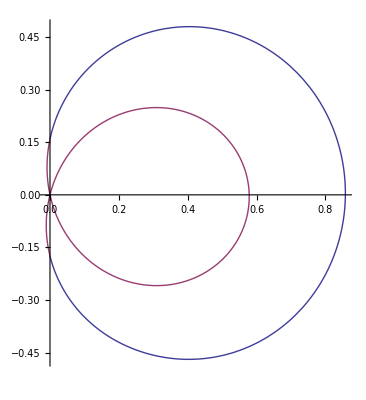

```mathematica
plboostk=ParametricPlot[{{vp Cos[alpha],vp Sin[alpha]},{vm Cos[alpha],vm Sin[alpha]}},{alpha,-Pi/2,Pi/2}]
```

```mathematica
v3p
v3m
v1p
v1m
```

0.158542-9.17708×10^-19 ⅈ

-0.174244+3.70634×10^-19 ⅈ

0.857959-1.76409×10^-18 ⅈ

0.578597-6.83091×10^-20 ⅈ

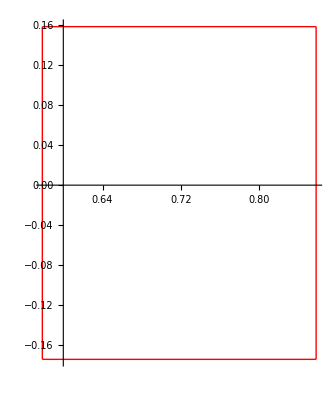

```mathematica
plotvpm=ParametricPlot[{{v1m,v3m+(v3p-v3m)t},{v1p,v3m+(v3p-v3m)t},{v1m+(v1p-v1m)t,v3m},{v1m+(v1p-v1m)t,v3p}},{t,0,1},PlotStyle->{RGBColor[1,0,0]}]
```

```mathematica
alphamaxes=FindRoot[D[vp Cos[alpha],alpha]==0,{alpha,{-1,1}}]
```

{alpha→{10.8709+3.41636×10^-19 ⅈ,3.13272-4.39438×10^-18 ⅈ}}

```mathematica
alphamaxes=FindRoot[vp Cos[alpha]==0,{alpha,{-1,1}}]
```

{alpha→{-1.5708-5.95359×10^-31 ⅈ,1.5708+2.47771×10^-26 ⅈ}}

```mathematica
alphamaxes[[1,2,2]]
```

1.5708+2.47771×10^-26 ⅈ

```mathematica
(* Comoving wave vector *)
kfld=kfl*{-vphase Sqrt[-gcov[[1,1]]],Cos[alpha] Sqrt[gcov[[2,2]]],0,Sin[alpha] Sqrt[gcov[[3,3]]]}/.consts;
kflu=Table[Sum[gcon[[ii,jj]]*kfld[[ii]],{ii,1,4}],{jj,1,4}]//.consts;

(* Boost uu to the fluid frame *)
uflu= LorentzBoostUpper[uu,uu,ud,wu,wd];
ufld=LorentzBoostLower[ud,uu,ud,wu,wd];

(* Boost bu to the fluid frame *)
bflu=LorentzBoostUpper[bu,uu,ud,wu,wd];
bfld=LorentzBoostLower[bd,uu,ud,wu,wd];

wfl=-(kfld.uflu)//.consts
ksq=(kfld.kflu+wfl^2)//.consts
kdotva=kfld.bflu/Sqrt[EF]//.consts
kdotva2=kdotva^2
```

1. kfl vphase+2.51897×10^-16 kfl Cos[alpha]+2.07538×10^-30 kfl Sin[alpha]

-1. kfl^2 vphase^2+1. kfl^2 Cos[alpha]^2+1. kfl^2 Sin[alpha]^2+(1. kfl vphase+2.51897×10^-16 kfl Cos[alpha]+2.07538×10^-30 kfl Sin[alpha])^2

2.88675 (3.39155×10^-18 kfl vphase-0.0166948 kfl Cos[alpha]+0.0799246 kfl Sin[alpha])

8.33333 (3.39155×10^-18 kfl vphase-0.0166948 kfl Cos[alpha]+0.0799246 kfl Sin[alpha])^2

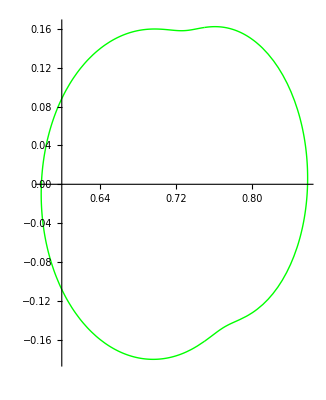

```mathematica
(* fast/slow modes *)
eq1x=0==(1/kfl^4*(wfl^4-wfl^2*(ksq*cms2+cs2*kdotva2)+ksq*cs2*kdotva2));
eq1x=Rationalize[eq1x];

(* Create comoving wave 4-vel from wfl/kphys *)
Clear[vphase]
sols1x=Solve[eq1x,vphase];
absvp=sols1x[[4,1,2]];
absvm=sols1x[[1,1,2]];
vpphys={ 1, absvp Cos[alpha],0,absvp Sin[alpha]}//.consts;
vmphys={ 1, absvm Cos[alpha],0,absvm Sin[alpha]}//.consts;
upu=vel3p2vel4u[vpphys];
upd=Table[Sum[gcov[[ii,jj]]*upu[[ii]],{ii,1,4}],{jj,1,4}]//.consts;
umu=vel3p2vel4u[vmphys]; 
umd=Table[Sum[gcov[[ii,jj]]*umu[[ii]],{ii,1,4}],{jj,1,4}]//.consts;

(* Boost comoving wave 4-vel to the lab frame *)
uplabu=InverseLorentzBoostUpper[upu,uu,ud,wu,wd];
uplabd=InverseLorentzBoostLower[upd,uu,ud,wu,wd];

umlabu=InverseLorentzBoostUpper[umu,uu,ud,wu,wd];
umlabd=InverseLorentzBoostLower[umd,uu,ud,wu,wd];

(* physical 4-velocity *)
uplabphys= {uplabu[[1]] Sqrt[-gcov[[1,1]]],uplabu[[2]] Sqrt[gcov[[2,2]]],uplabu[[3]] Sqrt[gcov[[3,3]]],uplabu[[4]] Sqrt[gcov[[4,4]]]}//.consts;

umlabphys= {umlabu[[1]] Sqrt[-gcov[[1,1]]],umlabu[[2]] Sqrt[gcov[[2,2]]],umlabu[[3]] Sqrt[gcov[[3,3]]],umlabu[[4]] Sqrt[gcov[[4,4]]]}//.consts;

(* physical 3-velocity, vphys = uphys/uphyst *)
vplabphys =uplabphys/uplabphys[[1]];
vmlabphys =umlabphys/umlabphys[[1]];

(* r-phi plane *)
plboostu=ParametricPlot[{{vplabphys[[2]],vplabphys[[4]]},{vmlabphys[[2]],vmlabphys[[4]]}},{alpha,-Pi/2,Pi/2},PlotStyle->{RGBColor[0,1,0]}]
```

```mathematica
sols1x//.consts/.alpha->0
sols1x//.consts/.alpha->Pi/2
absvp//.consts/.alpha->0
absvp//.consts/.alpha->Pi/2
```

{{vphase→-0.302804+2.41133×10^-18 ⅈ},{vphase→-0.031518-2.31664×10^-17 ⅈ},{vphase→0.031518+2.31664×10^-17 ⅈ},{vphase→0.302804-2.41133×10^-18 ⅈ}}

{{vphase→-0.244398+2.45382×10^-18 ⅈ},{vphase→-0.186949-3.20788×10^-18 ⅈ},{vphase→0.186949+3.20788×10^-18 ⅈ},{vphase→0.244398-2.45382×10^-18 ⅈ}}

0.302804-2.41133×10^-18 ⅈ

0.244398-2.45382×10^-18 ⅈ

```mathematica
(* WORK OUT GROUP 4-VELOCITY *)
```

```mathematica
dogroup=1;
```

```mathematica
If[dogroup==1,
Clear[omegalab,k1lab,k2lab,k3lab];
klabd={omegalab,k1lab,k2lab,k3lab}/.consts;
klabu=Table[Sum[gcon[[ii,jj]]*klabd[[ii]],{ii,1,4}],{jj,1,4}]//.consts;
wfl=-(klabd.uu)//.consts;
ksq=(klabd.klabu+wfl^2)//.consts;
kdotva=klabd.bu/Sqrt[EF]//.consts;
kdotva2=kdotva^2;
Disp=(wfl^4-wfl^2*(ksq*cms2+cs2*kdotva2)+ksq*cs2*kdotva2);
dxdlambdaconraw={D[Disp,klabd[[1]]],D[Disp,klabd[[2]]],D[Disp,klabd[[3]]],D[Disp,klabd[[4]]]};
omegalab = kd[[1]];
k1lab=kd[[2]];
k2lab=kd[[3]];
k3lab=kd[[4]];
vphasesols=Solve[Disp==0,vphase];
dxdlambdacon1=dxdlambdaconraw//.vphasesols[[1]];
dxdlambdacon2=dxdlambdaconraw//.vphasesols[[2]];
dxdlambdacon3=dxdlambdaconraw//.vphasesols[[3]];
dxdlambdacon4=dxdlambdaconraw//.vphasesols[[4]];
dxdlambdacon={dxdlambdacon1,dxdlambdacon2,dxdlambdacon3,dxdlambdacon4};
];
```

```mathematica
dxdlambdacon//.{alpha->0,k->1}
```

{{0.049268+1.03298×10^-19 ⅈ,0.0190042+4.65761×10^-20 ⅈ,-7.27208×10^-8-1.5223×10^-26 ⅈ,-0.0000827476-1.73219×10^-23 ⅈ},{-0.00321354-1.36618×10^-18 ⅈ,-0.00157651-7.0611×10^-19 ⅈ,-3.96758×10^-8-1.08182×10^-24 ⅈ,-0.0000451464-1.23099×10^-21 ⅈ},{0.00292356+1.34699×10^-18 ⅈ,0.00148803+6.42234×10^-19 ⅈ,-3.44285×10^-8+1.38261×10^-24 ⅈ,-0.0000391755+1.57325×10^-21 ⅈ},{-0.0195455+1.54154×10^-18 ⅈ,-0.0111795+8.1276×10^-19 ⅈ,-1.81711×10^-8-2.75856×10^-25 ⅈ,-0.0000206765-3.13892×10^-22 ⅈ}}

```mathematica
If[dogroup==1,
dxdlambdasq=dxdlambdacon*0;
vgroupcon=dxdlambdacon*0;
test=dxdlambdacon*0;
v3group=dxdlambdacon*0;
v3grouportho=dxdlambdacon*0;
v3grouporthoproj=dxdlambdacon*0;

(* choose direction for projection in lab frame to be same as Sasha choice *)
eprojcov=(kd)//.{alpha->beta}//.consts;
eprojcov[[1]]=0;
eprojcon=Table[Sum[eprojcov[[i]]*gcon[[i,j]],{i,1,4}],{j,1,4}]//.consts;
eprojcovnormalized=FullSimplify[eprojcov/Sqrt[eprojcov.eprojcon],{k>0}];

For[ii=1,ii≤4,ii++,
(* below should be -1 once normalized *)
dxdlambdasq[[ii]] = Sum[dxdlambdacon[[ii]][[i]]*dxdlambdacon[[ii]][[j]]*gcov[[i,j]],{i,1,4},{j,1,4}]//.consts;
vgroupcon[[ii]] = dxdlambdacon[[ii]]/Sqrt[-dxdlambdasq[[ii]]];
(* below should give -1 always *)
test[[ii]]=Sum[vgroupcon[[ii]][[i]]*vgroupcon[[ii]][[j]]*gcov[[i,j]],{i,1,4},{j,1,4}]//.consts;
(* obtain 3-velocity, defines frame! *)
v3group[[ii]]=vgroupcon[[ii]]/vgroupcon[[ii]][[1]];
v3grouportho[[ii]]=Table[v3group[[ii]][[i]]*Sqrt[-gcov[[i,i]]/gcov[[1,1]]],{i,1,4}]//.consts;
(* normalized projection *)
v3grouporthoproj[[ii]]=Sum[v3grouportho[[ii]][[i]]*eprojcovnormalized[[i]],{i,1,4}];
Print[ii];
];
];
```

1

2

3

4

```mathematica
(* see if -1  for particular case since now FullSimplify takes too long *)
test//.{alpha->0,k->1}
```

{-1.+1.47087×10^-33 ⅈ,-1.+1.63319×10^-31 ⅈ,-1.+9.24446×10^-33 ⅈ,-1.+4.02339×10^-32 ⅈ}

```mathematica
(* ensure independent of magnitude of k *)
(v3grouportho//.{k->1,alpha->0})-(v3grouportho//.{k->2,alpha->0})
```

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
(* prepare for plotting: k magnitude doesn't matter and choose beta=alpha for now *)
v3grouporthotoplot=v3grouportho//.{k->1};
```

```mathematica
v3grouporthotoplot//.{alpha->0}
```

{{0.+1. ⅈ,0.578597+2.04927×10^-19 ⅈ,-0.0000108465+2.04708×10^-23 ⅈ,-0.0123421+2.32934×10^-20 ⅈ},{0.+1. ⅈ,0.735877+1.67492×10^-17 ⅈ,0.0000907274-3.60973×10^-20 ⅈ,0.103237-4.10745×10^-17 ⅈ},{0.+1. ⅈ,0.763471-2.22464×10^-17 ⅈ,-0.0000865372+4.33462×10^-20 ⅈ,-0.0984691+4.93228×10^-17 ⅈ},{0.+1. ⅈ,0.857959+5.29228×10^-18 ⅈ,6.83174×10^-6+6.4253×10^-22 ⅈ,0.00777371+7.31123×10^-19 ⅈ}}

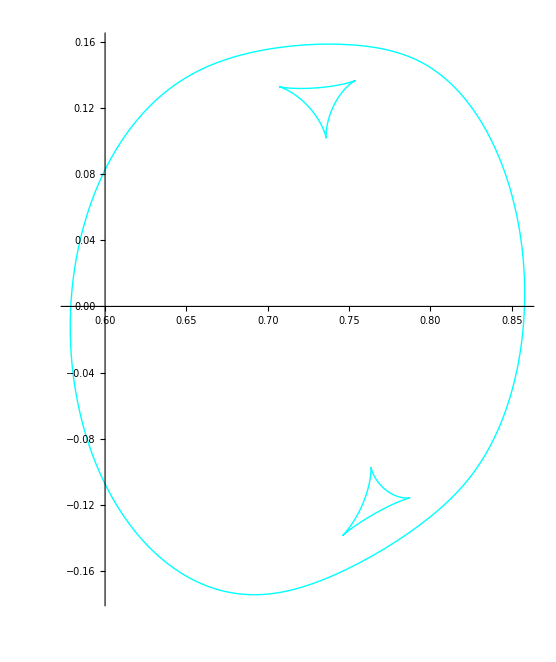

```mathematica
(* r-phi plane for the full quartic solution *)
plv3group=ParametricPlot[{{v3grouporthotoplot[[1]][[2]],v3grouporthotoplot[[1]][[4]]},{v3grouporthotoplot[[2]][[2]],v3grouporthotoplot[[2]][[4]]},{v3grouporthotoplot[[3]][[2]],v3grouporthotoplot[[3]][[4]]},{v3grouporthotoplot[[4]][[2]],v3grouporthotoplot[[4]][[4]]}},{alpha,-Pi/2,Pi/2},PlotStyle->{RGBColor[0,1,1]},PlotPoints->100]
```

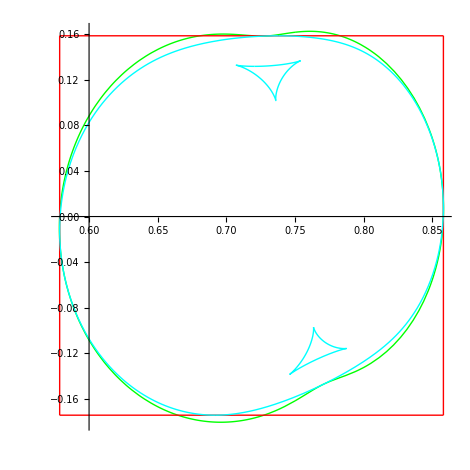

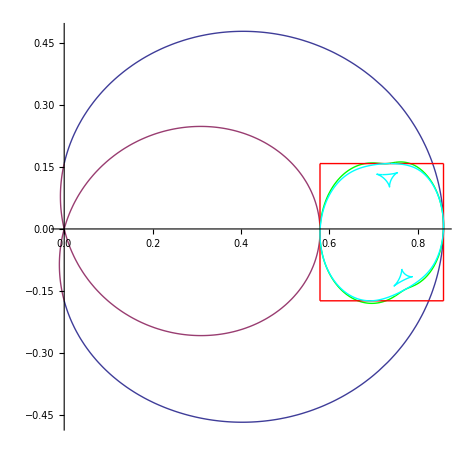

fig1.eps

```mathematica
fig=Show[plboostu,plotvpm,plv3group,AspectRatio->1]
fig=Show[plboostk,plboostu,plotvpm,plv3group,AspectRatio->1]
Export["fig1.eps",fig]
```

```mathematica
(* Done *)
```